## Tensor Definitions

```mathematica
(*Remove["Global`*"]*)
```

Mathematica build-in function like ‘Symmetrize[]’ and ‘TensorContract[]’ seem 
to work really slow or fail due to memory requirements on fully symmetric tensors 
with degree >10.
We define our own functions below based on a simply array data structure for fully symmetric tensors.

```mathematica
Clear[n,degree,idx,idx1,A,b,id3,IDX]
Unprotect[TensorDegree];

(*Every symmetric tensor can be identified with the help of a 2D array say a[N][3] where N is the total number of indepedent variables it has. So every row ie a[i] store the number of entries for x in a[i][1],for y in a[i][2] and for z in a[i][3]*)
IDXFull[n_]:=Flatten[Table[Table[{n-ii,ii-jj,jj},{jj,0,ii}],{ii,0,n}],1]

(*does the same thing as IDXFull but for trace free tensors*)
IDXtrfFull[n_]:=Flatten[Table[Table[{n-ii,ii-jj,jj},{jj,0,Min[ii,1]}],{ii,0,n}],1]

Do[
IDX[degree]=IDXFull[degree];
IDXtrf[degree]=IDXtrfFull[degree];
,{degree,0,40}]

(*given an array list, the following function counts the number of 1s, 2s and 3s*)
toIDX1[list_]:=Map[Count[list,#]&,{1,2,3}] (* Input cartesean indices, e.g. {1,1,2,1,3} *)

(*the Total of the list is the tensorial degree we are interested in. So list should be a 3X1 array and the following function will give us the n corresponding to which a[n] = list.*)
toIDX2[list_]:=Position[IDX[Total[list]],list]⟦1,1⟧ (* Input triple of #indices in {1,2,3} *)
(*same as above but for trace free tensors*)
toIDX3[list_]:=Position[IDXtrfFull[Total[list]],list]⟦1,1⟧ (* Input triple of #indices in {1,2,3} *)

(*Gives the tensor degree of a symmetric tensor.
CAUTION: the formulae is not valid for trace free tensors.*)
TensorDegree[A_]:=1/2 (-3+√(1+8 Length[A]))

id3={{1,0,0},{0,1,0},{0,0,1}};

DeltaValues[list_]:=Block[{a=list⟦1⟧,b=list⟦2⟧,c=list⟦3⟧},
If[OddQ[a]||OddQ[b]||OddQ[c],0,Multinomial[a/2,b/2,c/2]/Multinomial[a,b,c]]
];

(*applied deltavalues to all the components of an even degree tensor*)
DeltaTensor2[degree_?EvenQ]:=Map[DeltaValues,IDX[degree]];

(*What does this do?*)
SymTrace2[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree-2]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=Expand[Sum[A⟦toIDX2[IDX[degree-2]⟦jj⟧+2 id3⟦ii⟧]⟧,{ii,1,dim}]];
,{jj,1,length}];

res
];

SymTraces[A_,n_]:=Module[{res=A},
Do[res=SymTrace2[res],{ii,1,n}];
res
];

(*if the format of the input is IDX, then the output is also in IDX,
Assumes 3 dimensions. And so *)
(* contraction of a symmetric tensor A with Subscript[b, i] *)
SymDot2[A_,b_?VectorQ]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree-1]];
res=ConstantArray[0,length];
Do[
(*Lets take a particular term say Ai1i2..xbx. In the result only those components will appear in which x atleast appears once and that's why the addition of id3[[iis]]*)
res⟦jj⟧=Expand[Sum[A⟦toIDX2[IDX[degree-1]⟦jj⟧+id3⟦ii⟧]⟧b⟦ii⟧,{ii,1,dim}]];
,{jj,1,length}];

res
];

(*if the format of the input is IDX, then the output is also in IDX*)
(* full contraction of two symmetric tensors A, B with same degree *)
SymFullDot[A_,B_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
If[TensorDegree[B]≠degree,Return[0]];
length=Length[IDX[degree]];
res=0;
Do[
idx=IDX[degree]⟦jj⟧;
res+=Multinomial[idx⟦1⟧,idx⟦2⟧,idx⟦3⟧]A⟦jj⟧B⟦jj⟧;
,{jj,1,length}];

res
];

(* symmetric tensor product of a symmetric tensor A with Subscript[b, i] *)
SymProduct2[A_,b_?VectorQ]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
If[degree==0,Return[A⟦1⟧ b]];
length=Length[IDX[degree+1]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=
1/(degree+1)Sum[
If[(idx=IDX[degree+1]⟦jj⟧)⟦ii⟧>0,idx⟦ii⟧ A⟦toIDX2[idx-id3⟦ii⟧]⟧b⟦ii⟧,0],{ii,1,dim}];
,{jj,1,length}];

res
];

(* symmetric tensor product of a symmetric tensor A with Subscript[δ, ij] *)
SymProductDelta2[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree+2]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=1/((degree+2)(degree+1))Sum[
If[(idx=IDX[degree+2]⟦jj⟧)⟦ii⟧≥2,idx⟦ii⟧(idx⟦ii⟧-1)A⟦toIDX2[idx-2id3⟦ii⟧]⟧,0],{ii,1,dim}];
,{jj,1,length}];

res
];

(*converts a symmetric tensor into a trace free tensor*)
(* returns the tracefree part of a symmetric tensor, but with all components *)
SymTracefree[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res,trace,res1},
length=Length[IDX[degree]];
res=trace=A;
Do[
res1=trace=SymTrace2[trace];
Do[res1=SymProductDelta2[res1],{ll,1,kk}];
res+=(((-1)^kk degree!)/((degree-2kk)!2^kk kk!)∏_(jj=degree-kk)^(degree-1) 1/(2jj+1))res1;
,{kk,1,degree/2}];

res
];
```

```mathematica
trfEvaluate[A_,list_]:=Module[{a,b,c,m,dim=3,degree=(Length[A]-1)/2,length,res},
{a,b,c}=list;
m=Floor[c/2];
If[c≤1,
res=A⟦toIDX3[list]⟧,
res=(-1)^m Sum[Binomial[m,i]A⟦toIDX3[list+2i id3⟦1⟧+2(m-i) id3⟦2⟧-2m id3⟦3⟧]⟧,{i,0,m}]
];
res
];

(*say we have a trace free tensor, whose independent components are given then the following function will introduce those components in the list which have been negelected due to the trace free nature of the tensor. For eg. it will introduce -Rxx-Ryy for a second order tensor*)
trf2sym[A_]:=Map[Apply[trfEvaluate[A,{#1,#2,#3}]&,#]&,IDX[(Length[A]-1)/2]]

(*Pick the 2D variables from a list containing all the indices.The list will be obtained from the IDXtrf routine. freeindex is the total number of free indices in the tensor*)
Pick2D[freeindex_]:=Pick[IDXtrf[freeindex],Flatten[Join[{1},Table[{1,0},{k,1,freeindex}]]],1];
```

```mathematica
SymTensorForm[A_]:=Block[{degree=TensorDegree[A],length},
length=Length[IDX[degree]];
Table[Apply[{$[#1,#2,#3],A⟦ii⟧}&,IDX[degree]⟦ii⟧],{ii,1,length}]//TableForm
];
```

```mathematica
SymProductDelta2[SymProductDelta2[SymProductDelta2[Map[Apply[A[#1,#2,#3]&,#]&,IDX[1]]]]]
```

{A[1,0,0],1/7 A[0,1,0],1/7 A[0,0,1],1/7 A[1,0,0],0,1/7 A[1,0,0],3/35 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],3/35 A[0,0,1],3/35 A[1,0,0],0,1/35 A[1,0,0],0,3/35 A[1,0,0],1/7 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],1/7 A[0,0,1],1/7 A[1,0,0],0,1/35 A[1,0,0],0,1/35 A[1,0,0],0,1/7 A[1,0,0],A[0,1,0],1/7 A[0,0,1],1/7 A[0,1,0],3/35 A[0,0,1],3/35 A[0,1,0],1/7 A[0,0,1],1/7 A[0,1,0],A[0,0,1]}

```mathematica
Expand[SymTracefree[Map[Apply[A[#1,#2,#3]&,#]&,IDX[2]]]]
```

{-1/3 A[0,0,2]-1/3 A[0,2,0]+2/3 A[2,0,0],A[1,1,0],A[1,0,1],-1/3 A[0,0,2]+2/3 A[0,2,0]-1/3 A[2,0,0],A[0,1,1],2/3 A[0,0,2]-1/3 A[0,2,0]-1/3 A[2,0,0]}

```mathematica
Expand[SymTracefree[Map[Apply[#1+2.#2-3#3&,#]&,IDX[4]]]]
```

{-1.14286,1.14286,2.57143,3.42857,1.42857,-2.28571,3.14286,2.85714,-4.28571,-5.42857,-2.28571,4.28571,-1.14286,-5.71429,3.42857}

```mathematica
Expand[SymFullDot[SymTracefree[trf2sym[{Rxx,Rxy,0,Ryy,0}]],SymTracefree[trf2sym[{Sxx,Sxy,0,Syy,0}]]]]
```

2 Rxx Sxx+Ryy Sxx+2 Rxy Sxy+Rxx Syy+2 Ryy Syy

```mathematica
Normal[CoefficientArrays[Normal[CoefficientArrays[Expand[SymFullDot[SymTracefree[trf2sym[{Rxx,Rxy,0,Ryy,0}]],SymTracefree[trf2sym[{Sxx,Sxy,0,Syy,0}]]]],{Rxx,Rxy,Ryy}]]⟦2⟧,{Sxx,Sxy,Syy}]⟦2⟧]
```

{{2,0,1},{0,2,0},{1,0,2}}

```mathematica
Normal[CoefficientArrays[Normal[CoefficientArrays[Expand[SymFullDot[SymTracefree[trf2sym[{mxxx,mxxy,0,mxyy,0,myyy,0}]],SymTracefree[trf2sym[{nxxx,nxxy,0,nxyy,0,nyyy,0}]]]],{mxxx,mxxy,mxyy,myyy}]]⟦2⟧,{nxxx,nxxy,nxyy,nyyy}]⟦2⟧]
```

{{4,0,3,0},{0,6,0,3},{3,0,6,0},{0,3,0,4}}

## Basic Definitions

```mathematica
(*ref to manuels paper on fluxes for large moment system for a detailed expression*)
(*total tensorial degree including traces*)
iFullDegree[i_]=Floor[√(4i-3)-1];
(*number of traces C^2 has one trace*)
iTraces[i_]=Floor[(1+1/2 iFullDegree[i])^2]-i;
(*actual tensorial degree*)
iTensorDegree[i_]=iFullDegree[i]-2iTraces[i];
ii[s_,A_]=Floor[(A+2(s+1))/2](A+2(s+1)-Floor[(A+2(s+1))/2])-s;

(*i is as defined in the reference*)
NumberOfVariables2D[ntensors_]:=Sum[iTensorDegree[i]+1,{i,1,ntensors}];
NumberOfVariables3D[ntensors_]:=Sum[2iTensorDegree[i]+1,{i,1,ntensors}];
NumberOfFullTensors3D[ntensors_]:=Block[{m=iFullDegree[ntensors],frac},
m-(((m+1)(m+2)(m+3))/6.-Sum[2iTensorDegree[i]+1,{i,1,ntensors}])/(((m+1)(m+2))/2)
];

varName[s_,ix_,iy_,iz_]:=StringJoin["ρ",ToString[s],ConstantArray["x",ix],ConstantArray["y",iy],ConstantArray["z",iz]]


(*given a tensor W extract all the independed components in 2D in case of trace free situation*)
trfComponents2D[W_]:=Extract[W,Map[Position[IDX[TensorDegree[W]],#]⟦1⟧&,Pick[IDXtrf[TensorDegree[W]],Flatten[Join[{1},Table[{1,0},{k,1,TensorDegree[W]}]]],1]]]


trfVar2D[deg_,name_]:=Table[name[i],{i,1,deg+1}]
From2Dto3D[list_]:=Flatten[Join[{list⟦1⟧},Table[{list⟦k⟧,0},{k,2,Length[list]}]]]
```

## Create VarIdx

```mathematica
GetVarIdxComplete[Ntensors_]:=Block[{varIdx,varIdxComplete},

(*compute the tensor degree and the number of traces for every tensor in the system.
In all the coming computations, iTraces will be represented by a.sa*)
varIdx=Table[{iTraces[i],iTensorDegree[i]},{i,1,Ntensors}];

(*same as IDXFull but instead stores the value of the number of traces in the first argument of every list*)
varIdxComplete=Flatten[Table[Map[Join[{varIdx⟦n,1⟧},#]&,IDXFull[varIdx⟦n,2⟧]],{n,1,Length[varIdx]}],1];

{varIdx,varIdxComplete}]
```

## Radial Part

```mathematica
(*The quasi-laguerre polynomial given in Convergence of boundary value problem paper*)
Laguerre[n_,s_,x_]:=2^(n/2)√((Gamma[n+3/2]Gamma[n+s+3/2])/(n!s!))Sum[(-1)^p/Gamma[(n+p+3/2)] Binomial[s,p] x^(p+n/2),{p,0,s}];

Sonine[s_,n_,x_]:=√(s!(n+s)!)Sum[(-1)^p/(p!(s-p)!(p+n)!)x^p,{p,0,s}];

(*Quasi Sonine polynomial taken from Manuel's paper on explicit fluxes*)
QuasiSonine[n_,s_]:=√(((2n+1)!!)/(2n!)√π)Sonine[s,n+1/2,(Cx^2+Cy^2+Cz^2)/2] 1/(√2)^n;
```

## Angular part

```mathematica
TraceFreeCoord[idx_]:=Block[{nx=idx⟦2⟧,ny=idx⟦3⟧,nz=idx⟦4⟧,n=Total[idx⟦2;;-1⟧]},
Expand[(-1)^n/((2n-1)!!)(√(Cx^2+Cy^2+Cz^2))^(n+1)D[D[D[1/(√(Cx^2+Cy^2+Cz^2)),{Cx,nx}],{Cy,ny}],{Cz,nz}]]
];
```

## Hermite Basis

```mathematica
H[i_,c_]=1/(√Gamma[i+1] 2^(i/2))HermiteH[i,c/√2];

HSpcInt[n_,m_]:=Which[m==n,1/2,OddQ[m-n],1/(√(2 π))(√(n!m!))/(n!)(∑_(i=1)^n (2^(1/2 (1-2 i+m+n)) π)/(Gamma[(i-m)/2] Gamma[2-i+m] Gamma[1/2 (1+i-n)])+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];

(*θ0 has been considered to be 1*)
HermiteTuple[a_,b_,c_]:=H[a,Cx]H[b,Cy]H[c,Cz];

(*HermiteBasis[Ntensors_]:=Module[{tuple,MaxDegree,varIdx,varIdxComplete,basis},

{varIdx,varIdxComplete} = GetVarIdxComplete[Ntensors];
varIdx = Total[Transpose[varIdx],1];

(*maximum degree of the hermite polynomial to be considered*)
MaxDegree = Max[varIdx];

tuple = {};
Do[tuple=Join[tuple,IDXFull[ii]],{ii,0,MaxDegree}];

basis = Table[HermiteTuple[ii⟦1⟧,ii⟦2⟧,ii⟦3⟧],{ii,tuple}]
]*)

HermiteBasis[Degree_]:=Module[{tuple,basis},

tuple = IDXFull[Degree];

basis = Table[HermiteTuple[ii⟦1⟧,ii⟦2⟧,ii⟦3⟧],{ii,tuple}]
]


(*Project a function on a given set of Hermite basis*)
ProjectOnHermite[fun_,Basis_]:=Module[{w,result},


(*weighting function for our space*)
w = 1/(2π)^(3/2)Exp[(-(Cx^2+Cy^2+Cz^2))/2];

result = Table[NIntegrate[w fun Basis⟦ii⟧,{Cx,-8,8},{Cy,-8,8},{Cz,-8,8}],{ii,1,Length[Basis]}];

result

]

(*coeffs = expansion of coefficients and degree = degree of hermit basis with which the quantity has been projected*)
CheckProjection[coeffs_,Degree_,fun_]:=Module[{tuple},

Chop[Simplify[coeffs.HermiteBasis[6,Degree]-fun]]
]

(*Returns the maximum degree of a multivariate polynomial*)
ReturnMaxDegree[fun_]:=Max[Plus@@@CoefficientRules[#][[All,1]]]&@fun;
```

## Gauss Hermite Quadrature Routines

```mathematica
(*N is the number of quadrature points needed.*)
GaussHermiteQuadrature[points_]:=Module[{locations,weights,f0},

f0[c_]=1/(√(2π))Exp[-c^2/2];

(*location of the gauss quadrautre points*)
locations =Chop[ N[x/.{ToRules@Roots[H[points,x]==0,x]}]];

(*weights of the gauss quadrature*)
If[points == 1,weights = {1},weights = Table[(Coefficient[H[points,c],c^points]Integrate[f0[c] H[points-1,c]^2,{c,-∞,∞}])/(Coefficient[H[points-1,c],c^(points-1)](D[H[points,c],c]/.c->locations⟦ii⟧)(H[points-1,c]/.c->locations⟦ii⟧)),{ii,1,points}]];

{locations,weights}

]



(*f is the function which we wish to integrate and N is the number of quadrature points which we want to use in order to integrate*)
PerformNumericalIntegration1D[f_,M_]:=Module[{points,result},
points = GaussHermitePoints⟦M⟧;
result = 0;
Do[result=result+((f )/.{c->points⟦1⟧⟦ii⟧})*points⟦2⟧⟦ii⟧,{ii,1,Length[points⟦1⟧]}];
result

]

PerformNumericalIntegration3D[f_,GaussPoints_,Weights_]:=Module[{result},
result = 0;
Do[result=result+((f )/.{Cx->GaussPoints⟦ii⟧⟦1⟧,Cy->GaussPoints⟦ii⟧⟦2⟧,Cz->GaussPoints⟦ii⟧⟦3⟧})*Weights⟦ii⟧,{ii,1,Length[GaussPoints]}];
result

]
```

```mathematica
GaussHermitePoints = Table[GaussHermiteQuadrature[ii],{ii,1,20}];
```

### Convergence analysis for integration

```mathematica
Clear[Integrand]
Integrand[c_]:=H[4,c]^2;
TrialPoints = 20;
Error=Flatten[ConstantArray[0,{1,TrialPoints-1}]];
TrueValue = Integrate[Integrand[c]f0[c],{c,-∞,∞}];
Do[Error⟦ii-1⟧=Abs[TrueValue-PerformNumericalIntegration[Integrand[c],ii]],{ii,2,TrialPoints}];
```

```mathematica
TrueValue
```

1

```mathematica
Error
```

{0.833333,0.25,1.,2.22045×10^-16,8.88178×10^-16,2.22045×10^-16,4.44089×10^-16,5.77316×10^-15,1.14353×10^-14,1.08802×10^-14,3.39728×10^-14,5.10703×10^-15,1.82077×10^-14,1.01474×10^-13,2.62013×10^-14,6.01741×10^-14,3.11084×10^-13,3.55049×10^-13,8.85514×10^-13}

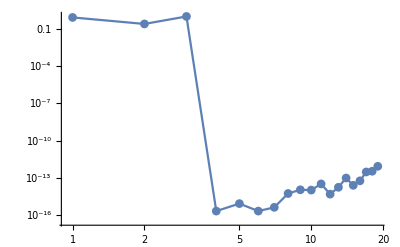

```mathematica
ListLogLogPlot[Error,Joined->True,PlotRange->Full,PlotMarkers->Automatic]
```

### Gauss Hermite points 3D

```mathematica
(*Gauss Hermite Quadrature points based upon the tensor product of quadrature rules in 1D*)
GaussHermite3DGrid[N_]:=Module[{points,weights,GaussPoints,GaussWeights},
points = GaussHermitePoints⟦N⟧⟦1⟧;
weights = GaussHermitePoints⟦N⟧⟦2⟧;
GaussPoints = ConstantArray[0,{Length[points]*Length[points]*Length[points],3}];
GaussWeights = Flatten[ConstantArray[0,{Length[points]*Length[points]*Length[points],1}]];
(*convert to (x,y,z) 3D*)
Do[Do[Do[GaussPoints⟦kk+(jj-1)*Length[points]+(ii-1)*Length[points]^2⟧={points⟦kk⟧,points⟦jj⟧,points⟦ii⟧};
GaussWeights⟦kk+(jj-1)*Length[points]+(ii-1)*Length[points]^2⟧=weights⟦kk⟧*weights⟦jj⟧*weights⟦ii⟧;,{kk,1,Length[points]}],{jj,1,Length[points]}],{ii,1,Length[points]}];

{GaussPoints,GaussWeights}

]

(*Gauss Hermite Quadrature points based upon a line in 3D*)
GaussHermite3DLine[N_]:=Module[{points,weights,GaussPoints,GaussWeights},
points = GaussHermitePoints⟦N⟧⟦1⟧;
weights = GaussHermitePoints⟦N⟧⟦2⟧;

(*convert to (x,y,z) 3D*)
Do[points⟦ii⟧={points⟦ii⟧,points⟦ii⟧,points⟦ii⟧};
weights⟦ii⟧=weights⟦ii⟧^3,{ii,1,Length[points]}];

{points,weights}

]
```

## Basis function (Spherical Harmonics)

### Psi

```mathematica
ψ[idx_]:=Module[{n,s,result},

(*The number of traces in the tensor*)
s = idx⟦1⟧;

(*The total tensorial degree*)
n = Total[idx⟦2;;-1⟧];

result = Laguerre[n,s,(Cx^2+Cy^2+Cz^2)/(2θ0)]*TraceFreeCoord[idx];
result

]
```

### Distribution function

```mathematica
(*get the contribution into f from a particular tensor*)
GetfTensor[n_,s_]:=Module[{allComponents,allComponentsTrf,varIdxComplete,PsiList,coeffSym,replaceTrf,result,Var2D},

(*all components in the tensors*)
allComponents = Map[w[#]&,IDX[n]];

(*conversion to trace free tensors*)
allComponentsTrf = trf2sym[Map[w[#]&,IDXtrf[n]]];

(*trace free variables in 2D*)
Var2D = Map[w[#]&,Pick[IDXtrf[n],Flatten[Join[{1},Table[{1,0},{k,1,n}]]],1]];

(*replacement for trace free variables*)
replaceTrf = Table[allComponents⟦ii⟧->allComponentsTrf⟦ii⟧,{ii,1,Length[allComponents]}];

varIdxComplete=Map[Join[{s},#]&,IDXFull[n]];

(*list of all the basis functions*)
PsiList =Simplify[ Map[ψ[#]&,varIdxComplete]/.{θ0->1}];

(*coefficients for symmetric tensors*)
coeffSym=Table[coeffEntropySym[ii⟦1⟧],{ii,allComponents}];

(*contribution into the distribution function from this particular tensor*)
result = allComponents*PsiList;

(*account for the symmetricity of the tensors*)
result = result*coeffSym;

(*account for the trace free nature of the tensors*)
result = result/.replaceTrf;
result=Simplify[Total[result]];

(*Pick up only those components which have a 2D contribution*)
result=Coefficient[result,Var2D];

result
]

Getf[Ntensors_]:=Module[{varIdx,varIdxComplete,result,coeffSym,varTrf,n,s,tempvarTrf},

{varIdx,varIdxComplete }= GetVarIdxComplete[Ntensors];

result = Flatten[Table[GetfTensor[ii⟦2⟧,ii⟦1⟧],{ii,varIdx}],1];

result
]
```

## Distribution function

```mathematica
Clear[f0]
```

```mathematica
f0=1/(2π)^(3/2)Exp[(-(Cx^2+Cy^2+Cz^2))/2];
```

### G20

```mathematica
(*a list of all the basis functions*)
Listψ = Getf[6];

(*The coefficients appearing in the hermite expansion*)
coefficients=Quiet[Table[ProjectOnHermite[Listψ⟦ii⟧,HermiteBasis[6,ReturnMaxDegree[Listψ⟦ii⟧]]],{ii,1,Length[Listψ]}]];
```

```mathematica
Chop[Table[CheckProjection[coefficients⟦ii⟧,ReturnMaxDegree[Listψ⟦ii⟧],Listψ⟦ii⟧],{ii,1,Length[coefficients]}],10^-7]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0}

### Transfer matrix

```mathematica
(*Transf Part for the nth degree tensors appearing in G20*)
Transf0 = 1;
Transf1=IdentityMatrix[2];
Transf2 = Transpose[coefficients⟦{4,5,6,7},{1,2,4,6}⟧];
Transf3 = Transpose[coefficients⟦8;;-1,{1,2,4,6,7,9}⟧];
```

```mathematica
TransfMat20 = ConstantArray[0,{13,13}];
TransfMat20⟦1,1⟧=Transf0;
TransfMat20⟦{2,3},{2,3}⟧=Transf1;
TransfMat20⟦{4,5,6,7},{4,5,6,7}⟧=Transf2;
TransfMat20⟦{8,9,10,11,12,13},{8,9,10,11,12,13}⟧=Transf3;
```

```mathematica
TransfMat20//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.57735 | 1. | 0. | 2.61554×10^-13 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0. | 0. | 1.41421 | 0. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.57735 | 2.61553×10^-13 | 0. | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.57735 | -1. | 0. | -1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.774597 | 0. | 1. | 1.28394×10^-23 | 2.71649×10^-16 | 1.00198×10^-23
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | -0.447214 | 0. | 1.73205 | 0. | -8.76255×10^-11
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.447214 | 0. | -8.76256×10^-11 | 0. | 1.73205 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.447214 | 0. | -1.73205 | 0. | -1.73205 | 0.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | -0.774597 | 4.53417×10^-23 | 3.55863×10^-10 | 4.61058×10^-22 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | -0.447214 | 0. | -1.73205 | 0. | -1.73205)

### Flux Matrix Transformation

```mathematica
AxHermite = TransfMat20.Ax20New.Inverse[TransfMat20];
AyHermite=TransfMat20.Ay20New.Inverse[TransfMat20];
```

```mathematica
Chop[AxHermite,10^-7]//MatrixForm
```

(0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 0 | 1.41421 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.41421 | 0 | 0 | 0 | 0 | 0 | 1.73205 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 1.41421 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1.73205 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.41421 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Chop[AyHermite,10^-7]//MatrixForm
```

(0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1. | 0 | 0 | 0 | 0 | 1.41421 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.41421 | 0 | 0 | 0
0 | 0 | 1.41421 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.73205 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.41421 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.73205 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
GenerateProjector2D
```

{{nx^2,2 nx ny,ny^2},{-nx ny,nx^2-ny^2,nx ny},{ny^2,-2 nx ny,nx^2}}

```mathematica
N[Roots[H[4,c]==0,c]]
```

c==0.741964||c==-0.741964||c==2.33441||c==-2.33441

```mathematica
Chop[N[Eigenvalues[AxHermite]]]
```

{2.33441,-2.33441,1.73205,-1.73205,1.,-1.,1.,-1.,-0.741964,0.741964,0,0,0}

```mathematica
N[Roots[H[3,c]==0,c]]
```

c==0.||c==1.73205||c==-1.73205

```mathematica
N[Roots[H[2,c]==0,c]]
```

c==1.||c==-1.

```mathematica
N[Roots[H[1,c]==0,c]]
```

c==0.

### Tuple Indices

```mathematica
indexG20=Flatten[Join[{IDXFull[0],IDXFull[1]⟦{1,2}⟧,IDXFull[2]⟦{1,2,4,6}⟧,IDXFull[3]⟦{1,2,4,6,7,9}⟧}],1]
```

{{0,0,0},{1,0,0},{0,1,0},{2,0,0},{1,1,0},{0,2,0},{0,0,2},{3,0,0},{2,1,0},{1,2,0},{1,0,2},{0,3,0},{0,1,2}}

```mathematica
OddindexG20 = indexG20⟦{2,5,8,10,11}⟧;
EvenindexG20 = indexG20⟦{1,3,4,6,7,9,12,13}⟧;
```

```mathematica
OddindexG20
```

{{1,0,0},{1,1,0},{3,0,0},{1,2,0},{1,0,2}}

```mathematica
EvenindexG20
```

{{0,0,0},{0,1,0},{2,0,0},{0,2,0},{0,0,2},{2,1,0},{0,3,0},{0,1,2}}

### Quadrature points

```mathematica
EigenVector = Table[HermiteTuple[ii⟦1⟧,ii⟦2⟧,ii⟦3⟧],{ii,indexG20}];
EigenValues = Chop[N[Eigenvalues[AxHermite]]];
```

```mathematica
Chop[Simplify[(AxHermite.EigenVector-EigenValues⟦3⟧EigenVector)/.{Cx->EigenValues⟦3⟧}],10^-6]//MatrixForm
```

(0
0
0
0
0
0
0
2.44949
0
1.41421-1.41421 Cy^2
1.41421-1.41421 Cz^2
2.12132 Cy-0.707107 Cy^3
Cy (1.22474-1.22474 Cz^2))

```mathematica
EigenValues
```

{2.33441,-2.33441,1.73205,-1.73205,1.,-1.,1.,-1.,-0.741964,0.741964,0,0,0}

```mathematica
PerformNumericalIntegration3D[Listψ⟦1⟧Listψ⟦1⟧,QuadPoints,QuadWeights]
```

2.99306

```mathematica
Integrate[Listψ⟦5⟧Listψ⟦5⟧f0,{Cx,-∞,∞},{Cy,-∞,∞},{Cz,-∞,∞}]
```

2

### 3 moment quadrature

```mathematica
TrialA = Table[{Integrate[Listψ⟦ii⟧Cx Listψ⟦1⟧f0,{Cx,-∞,∞},{Cy,-∞,∞},{Cz,-∞,∞}],Integrate[Listψ⟦ii⟧Cx Listψ⟦2⟧f0,{Cx,-∞,∞},{Cy,-∞,∞},{Cz,-∞,∞}],Integrate[Listψ⟦ii⟧Cx Listψ⟦3⟧f0,{Cx,-∞,∞},{Cy,-∞,∞},{Cz,-∞,∞}]},{ii,1,3}];
```

```mathematica
TrialA//MatrixForm
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 0)

```mathematica
Listψ⟦{1,2,3}⟧
```

{1,Cx,Cy}

```mathematica
N[Eigenvalues[TrialA]]
```

{-1.,1.,0.}

```mathematica
TrialEigenVector={1,1,Cy};
TrialA.TrialEigenVector-TrialEigenVector
```

{0,0,-Cy}